## Importing data

```mathematica
f77Eform[x_?NumericQ,fw_Integer,ndig_Integer]:=Module[{sig,s,p,ps},{s,p}=MantissaExponent[x];
{sig,ps}={ToString[Round[10^ndig Abs[s]]],ToString[Abs[p]]};
StringJoin@@Join[Table[" ",{fw-ndig-7}],If[x<0,"-"," "],{"0."},{sig},Table["0",{ndig-StringLength[sig]}],{"E"},If[p<0,{"-"},{"+"}],Table["0",{2-StringLength[ps]}],{ps}]];
```

```mathematica
SetDirectory[StringJoin[NotebookDirectory[]]];
```

```mathematica
he={};
StringJoin[NotebookDirectory[],"df/He4.ddp.ddp_he0_k.ddt.df"];
Import[%,"Table"];
Drop[%,None,{2,3}];
AppendTo[he,%];

StringJoin[NotebookDirectory[],"df/He4.ddp.ddp_he0_p.ddt.df"];
Import[%,"Table"];
Drop[%,None,{2,3}];
AppendTo[he,%];

StringJoin[NotebookDirectory[],"df/He4.ddp.ddp_he0_tot.ddt.df"];
Import[%,"Table"];
Drop[%,None,{2,3}];
AppendTo[he,%];
```

### Lithium - 6

```mathematica
li={};
StringJoin[NotebookDirectory[],"df/He4.ddp.ddp_li0_k.ddt.df"];
Import[%,"Table"];
Drop[%,None,{2,3}];
AppendTo[li,%];

StringJoin[NotebookDirectory[],"df/He4.ddp.ddp_li0_p.ddt.df"];
Import[%,"Table"];
Drop[%,None,{2,3}];
AppendTo[li,%];

StringJoin[NotebookDirectory[],"df/He4.ddp.ddp_li0_tot.ddt.df"];
Import[%,"Table"];
Drop[%,None,{2,3}];
AppendTo[li,%];
```

### Berillium - 9

```mathematica
be={};
StringJoin[NotebookDirectory[],"df/He4.ddp.ddp_be0_p.ddt.df"];
Import[%,"Table"];
Drop[%,None,{2,3}];
AppendTo[be,%];

StringJoin[NotebookDirectory[],"df/He4.ddp.ddp_be0_k.ddt.df"];
Import[%,"Table"];
Drop[%,None,{2,3}];
AppendTo[be,%];
```

## Plot Folding Potentials

```mathematica
ListLogPlot[{Abs[he⟦2⟧],Abs[he⟦1⟧]},PlotRange->{{0,8.0},{0.01,60}},Joined->True,AspectRatio->1,Frame->True,ImageSize->Small,FrameLabel->{"r, fm","-V^DF(r), MeV"},PlotLabel->"^6He+α"]
Export["he_df.pdf",%,"pdf"];
```

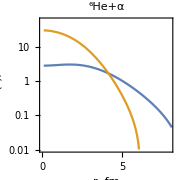

```mathematica
ListLogPlot[{Abs[li⟦2⟧],Abs[li⟦1⟧]},PlotRange->{{0,8.0},{0.01,60}},Joined->True,AspectRatio->1,Frame->True,ImageSize->Small,FrameLabel->{"r, fm","-V^DF(r), MeV"}, PlotLabel->"^6Li+α"]
Export["li_df.pdf",%,"pdf"];
```

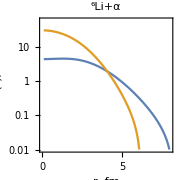

```mathematica
ListLogPlot[{Abs[be⟦2⟧],Abs[be⟦1⟧]},PlotRange->{{0,8.0},{0.01,60}},Joined->True,AspectRatio->1,Frame->True,ImageSize->Small,FrameLabel->{"r, fm","-V^DF(r), MeV"},PlotLabel->"^9Be+α"]
Export["be_df.pdf",%,"pdf"];
```

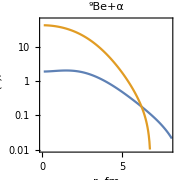

## Export to fort.4 file

```mathematica
li⟦3,All,2⟧;
f77Eform[#,8,8]&/@%;
Transpose@{%,%};
Export["fort_li.4",%,"Table"]
```

fort_li.4